Абсолютная точность Рунге-Кутты

0.0878146

Оценка погрешности метода Рунге-Кутты методом Рунге

4.75467

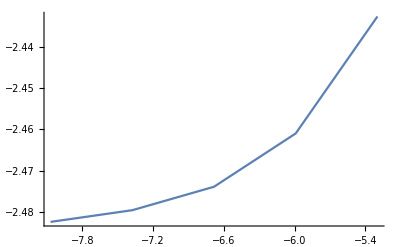

График решения (Метод:Рунге)

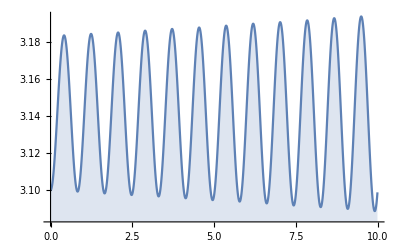

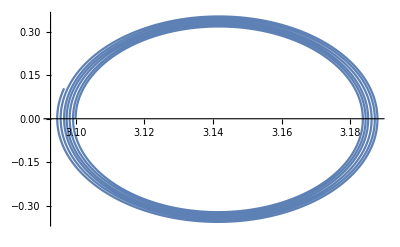

Условие устойчивости НЕ ВЫПОЛНЕНО

```mathematica
(*SMassiv1=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\data\\Eiler.txt" ];*)
SMassiv2=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge.txt" ];
(*Massiv1=ToExpression[SMassiv1][[1]];(*Эйлер*)*)
Massiv2=ToExpression[SMassiv2][[1]];(*Рунге-Кутты*)
Temp=NDSolve[{y''[x]== (3/(2*10))*(386 - 0.5*5.3*Sin[5.3*x])*Sin[y[x]],y[0]==3.1,y'[0]==0},y,{x,0,10}];
Massiv =Table[{x,Evaluate[y[x]/.Temp]},{x,0,10,0.01}];(*Точное решение*)
(*Точность решения 1*)
(*Print["Абсолютная точность Эйлера"];
MAX1 = Max[Table[Abs[Massiv[[i,2]]-Massiv1[[i,2]]],{i, 1, 1000}]](*Точность решения (Метод:Эйлера)*)*)
Print["Абсолютная точность Рунге-Кутты"];
MAX2 = Max[Table[Abs[Massiv[[i,2]]-Massiv2[[i,2]]],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
(*Оценка погрешности*)
P1=2;

(*SMassiv11=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\data\\Eiler_1.txt" ];*)
SMassiv22=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge1.txt" ];
(*Massiv11=ToExpression[SMassiv11][[1]];(*Эйлер*)*)
Massiv22=ToExpression[SMassiv22][[1]];(*Рунге-Кутты*)
(*Print["Оценка погрешности метода Эйлера методом Рунге"];*)
(*MAX11 = Max[Table[Abs[(2^P1/(2^P1-1))*(Massiv11[[2i,2]]-Massiv1[[i,2]])],{i, 1, 1000}]]*)(*Точность решения (Метод:Эйлера)*)
Print["Оценка погрешности метода Рунге-Кутты методом Рунге "];
MAX22 = Max[Table[Abs[(2^P1/(2^P1-1))(Massiv22[[2i,2]]-Massiv2[[i,2]])],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
(*Сходимость*)
(*SMoreMassiv1=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\data\\Eiler_All.txt"  ];*)
SMoreMassiv2=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge_all.txt"  ];
(*MoreMassiv1=ToExpression[SMoreMassiv1];(*Эйлер*)*)
MoreMassiv2=ToExpression[SMoreMassiv2];(*Рунге-Кутты*)
(*Graph1 = Table[{Log[MoreMassiv1[[k,2,1]]],Log[Max[Table[Abs[(Massiv[[i,2]]-MoreMassiv1[[k,2^(k-1)*i,2]])],{i, 1, 1000}]]]},{k,1,5}];*)
Graph2 = Table[{Log[MoreMassiv2[[k,2,1]]],Log[Max[Table[Abs[(Massiv[[i,2]]-MoreMassiv2[[k,2^(k-1) i,2]])],{i, 1, 1000}]]]},{k,1,5}];
Print["График сходимости"]
ListLinePlot[Graph2]
(*Print["График сходимости"]
ListLinePlot[{Graph1,Graph2}]*)
(*Print["График решения (Метод:Эйлера)"]
ListLinePlot[{Massiv1, Massiv},Filling->Axis]*)
Print["График решения (Метод:Рунге)"]
ListLinePlot[{Massiv2, Massiv},Filling->Axis]
(*SMoreMassiv1=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\data\\EilerDy.txt"  ];*)
SMoreMassiv2=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge1.txt"];
(*DyMassiv1=ToExpression[SMoreMassiv1][[1]];(*Эйлер*)*)
DyMassiv2=ToExpression[SMoreMassiv2][[1]];(*Рунге-Кутты*)
(*FazT1= Table[{Massiv1[[i,2]], DyMassiv1[[i,2]]},{i,1,1000}];*)
FazT2= Table[{Massiv2[[i,2]],DyMassiv2[[i,2]]},{i,1,1000}];
(*ListLinePlot[FazT1]*)
ListLinePlot[FazT2]
If[ Min[Table[DyMassiv2[[i,2]],{i,1,1000}]]<0,Print["Условие устойчивости НЕ ВЫПОЛНЕНО"], Print["Условие устойчивости ВЫПОЛНЕНО"]]
```